```mathematica
Subscript[w, ab]=300;
Subscript[w, bc]=100;
Subscript[Γ, a]=1;Subscript[Γ, b]=1;
q1=-I Subscript[Γ, b]/2+Subscript[w, bc];
q2=
```

```mathematica
Integrate[-Exp[I q 1]/((I(k+q-Subscript[w, ab])-Subscript[Γ, a]/2)(I(q-Subscript[w, bc])-Subscript[Γ, b]/2)),{q,-Infinity,Infinity}]
```

ConditionalExpression[(4 ⅈ ⅇ^((1/2+300 ⅈ)-ⅈ k) π)/(400-2 k),Im[k]<-1/2]

```mathematica
Integrate[- (Exp[I(Subscript[v, k]-Subscript[w, ab])t-Subscript[Γ, a] t/2]-Exp[-Subscript[Γ, b]t/2])/(I(Subscript[v, k]-Subscript[w, ab])-1/2(Subscript[Γ, a]-Subscript[Γ, b])),{t,0,T}]//Simplify
```

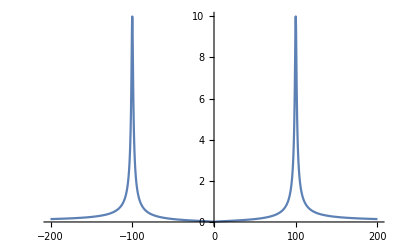

```mathematica
Plot[Abs[(√Abs[k])/(I(Abs[k]-100)-1)],{k,-200,200},PlotRange->All]
```

```mathematica
fx=1/Sqrt[2π] Integrate[Sqrt[Abs[k]]/(I (Abs[k]-100)-1) E^(-I k x),{k,-∞,∞},GenerateConditions->False]
```

-1/(√20002 √(-ⅈ x) √(ⅈ x))ⅇ^((-1-100 ⅈ) x) (ⅈ √10001 ⅇ^((1+100 ⅈ) x) √(-ⅈ x)+ⅈ √10001 ⅇ^((1+100 ⅈ) x) √(ⅈ x)+(1+100 ⅈ) ⅇ^((2+200 ⅈ) x) √((-100-ⅈ) π) √(-ⅈ x) √(ⅈ x)-(1+100 ⅈ) ⅇ^((2+200 ⅈ) x) √((-100-ⅈ) π) √(-ⅈ x) √(ⅈ x) Erf[(√10001 √(-ⅈ x))/(√(-100-ⅈ))]+√((1000100-10001 ⅈ) π) √(-ⅈ x) √(ⅈ x) Erfc[√(-100+ⅈ) √(ⅈ x)])

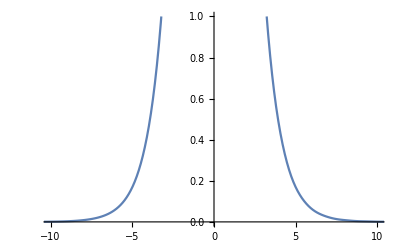

```mathematica
Plot[Abs[fx], {x,-200,200},PlotRange->{{-10,10},{0,1}}]
```

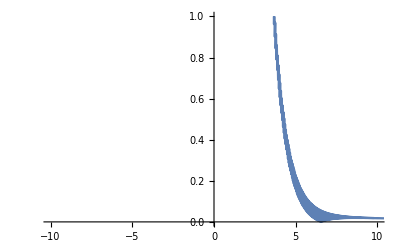

```mathematica
f[k_]:=(√Abs[k])/(I(Abs[k]-100)-1);
sampling=Array[f,100000,{0,200}];
ListLinePlot[Abs[InverseFourier[sampling]],PlotRange->{{-10,10},{0,1}}, DataRange->{0,800Pi}]
```

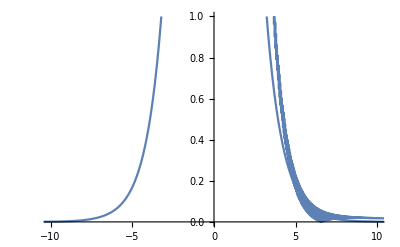

```mathematica
Show[Out[94],Out[78]]
```

```mathematica
Subscript[w, ab]=300;
Subscript[w, bc]=100;
Subscript[Γ, a]=1;Subscript[Γ, b]=1;
f[k_,q_]:=(-√(Abs[k]Abs[q]))/((I(Abs[q]+Abs[k]-Subscript[w, ab])-0.5 Subscript[Γ, a])(I(Abs[q]-Subscript[w, bc])-0.5 Subscript[Γ, b]));
Plot3D[Abs[f[k,q]],{k,-1000,1000},{q,-300,300},PlotRange->All,AxesLabel->{k,q}]
```

```mathematica
sampling=Array[f,{3600,1200},{{-600,600},{-200,200}}];
Dimensions[sampling]
```

{3600,1200}

```mathematica
ListPlot3D[Abs[InverseFourier[sampling]],PlotRange->All,AxesLabel->{x1,x2}]
```

```mathematica
Integrate[Exp[I x]/(x+I),{x,-Infinity, Infinity}]
```

0